```mathematica
elementList={"Sc"->1,"Ti"->2,"V"->3,"Cr"->4,"Mn"->5,"Fe"->6,"Co"->7,"Ni"->8,"Cu"->9,"Zn"->10,"Y"->11,"Zr"->12,"Nb"->13,"Mo"->14,"Tc"->15,"Ru"->16,"Rh"->17,"Pd"->18,"Ag"->19,"Hf"->20,"Ta"->21,"W"->22,"Re"->23,"Os"->24,"Ir"->25,"Pt"->26,"Au"->27};
elements=List@@@elementList//Transpose//First;
targets = {ORR -> -1.51, CORedCO -> -1.20, ORedCO -> -1.25};

myPrint[list_]:=ToString[Row[{"(",Row[NumberForm[#,{4,3}]&/@list," "],")"}]]
returnValue[row_, col_, myTable_] := myTable[[row,col]]
```

## Parse Data:

```mathematica
data=Import["/home/marco/fridbDemo/allresults.json"];
```

Parse 38 atom NP oxygen binding energy:

```mathematica
atoms32=Select[data,StringCases[#[[1]],"32"]≠{}&];
atoms32Binding=Select[atoms32,StringCases[#[[1]],"Binding"]≠{}&];
dataall={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms32Binding)/.elementList;
tab=Table[Cases[dataall,{m,n,_}][[;;,3]],{m,1,27},{n,1,27}]//MatrixForm;
smallBindingTable = Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}]//MatrixForm;
```

Parse 79 atom NP oxygen:

```mathematica
atoms79=Select[data,StringCases[#[[1]],"60"]≠{}&];
atoms79Binding=Select[atoms79,StringCases[#[[1]],"Binding"]≠{}&];
dataall79={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms79Binding)/.elementList;
tab=Table[Cases[dataall79,{m,n,_}][[;;,3]],{m,1,27},{n,1,27}]//MatrixForm;
bigBindingTable = Table[With[{x=Cases[dataall79,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}]//MatrixForm;
```

Parse 79 atom NP Segregation Energy

```mathematica
atoms79Segregation=Select[atoms79,StringCases[#[[1]],"Segregation Energy"~~EndOfString]≠ {}&];
dataSegFormat={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms79Segregation)/.elementList;
bigSegTable = Table[With[{x=Cases[dataSegFormat,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];

atoms79SegregationOxygen=Select[atoms79,StringCases[#[[1]],"Segregation Energy With Oxygen"~~EndOfString]≠ {}&];
dataSegWithOxygenFormat={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms79SegregationOxygen)/.elementList;
bigSegTableOxygen = Table[With[{x=Cases[dataSegWithOxygenFormat,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
```

```mathematica
atoms38Segregation=Select[atoms32,StringCases[#[[1]],"Segregation Energy"~~EndOfString]≠ {}&];
data38SegFormat={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms38Segregation)/.elementList;
smallSegTable = Table[With[{x=Cases[data38SegFormat,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];

atoms38SegregationOxygen=Select[atoms32,StringCases[#[[1]],"Segregation Energy With Oxygen"~~EndOfString]≠ {}&];
data38SegWithOxygenFormat={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms38SegregationOxygen)/.elementList;
smallSegTableOxygen = Table[With[{x=Cases[data38SegWithOxygenFormat,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
```

## Make Matrix Plots:

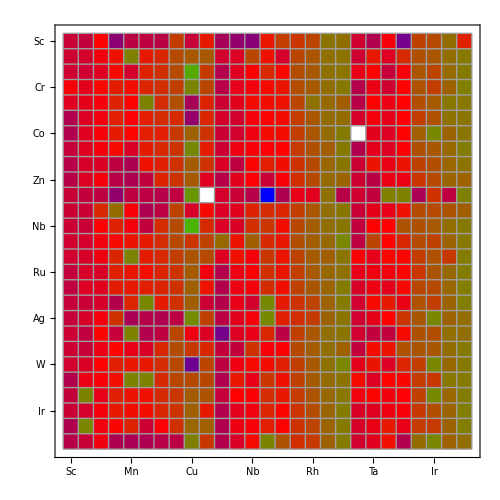

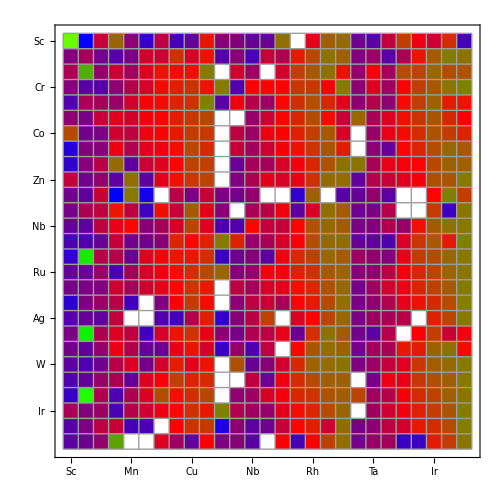

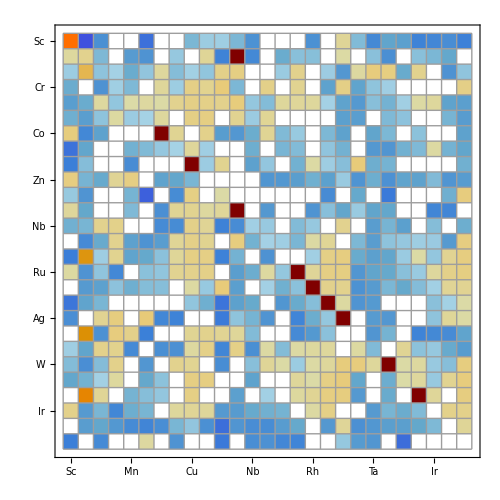

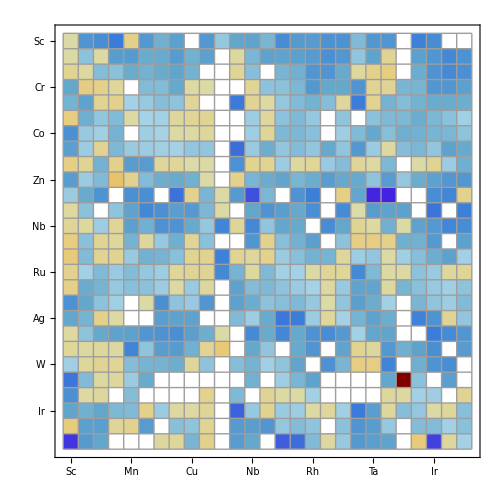

```mathematica
MatrixPlot[smallBindingTable,ColorFunction->(Blend[{Blue, Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]

MatrixPlot[bigBindingTable,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]

MatrixPlot[bigSegTable, Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]

MatrixPlot[bigSegTableOxygen, Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]
```

## Make Bar Charts:

### These statements are used to filter out spurious binding energies. Then nanoparticle removed has its corresponding label removed, so that the bar chart bars and their labes line up correctly

{}

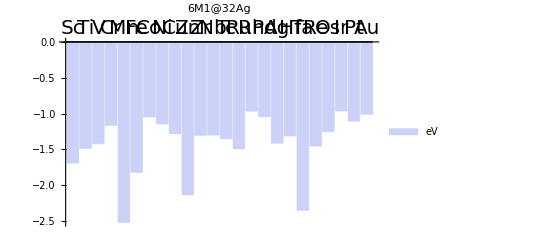

{{Sc},{Ti},{V},{Cr},{Mn},{Fe},{Co},{Ni},{Cu},{Zn},{Y},{Zr},{Nb},{Mo},{Tc},{Ru},{Rh},{Pd},{Ag},{Hf},{Ta},{W},{Re},{Os},{Ir},{Pt},{Au}}

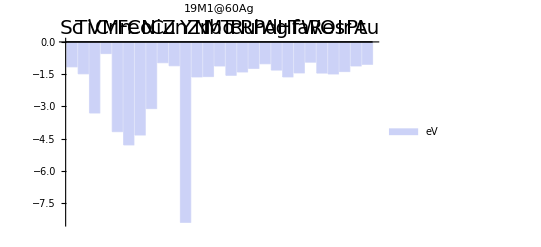

{{Sc},{Ti},{V},{Cr},{Mn},{Fe},{Co},{Ni},{Cu},{Zn},{Y},{Zr},{Nb},{Mo},{Tc},{Ru},{Rh},{Pd},{Ag},{Hf},{Ta},{W},{Re},{Os},{Ir},{Pt},{Au}}

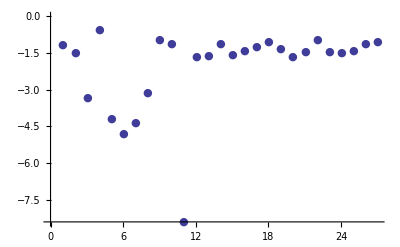

-Graphics-

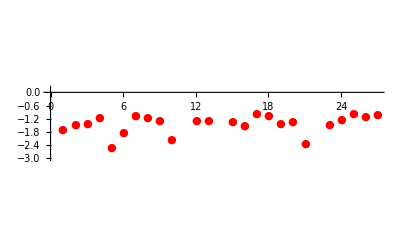

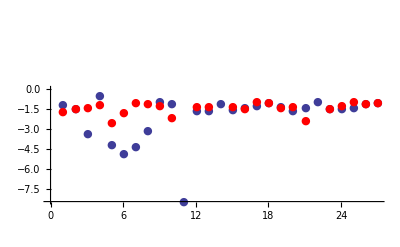

{0.528839,0.00008181,-1.8915,0.6229,-1.66226,-2.97975,-3.29121,-1.96083,0.313333,1.02347,1.6646,-0.328496,-0.314616,-5.48928,-0.205317,0.0908144,-0.267932,0.0252885,0.100085,-0.317968,0.904503,-5.36616,0.00134848,-0.242626,-0.417037,-0.0155537,-0.0349103}

```mathematica
placeholder =DeleteCases[Map[ If[# >0 || # <-10 ,0,#] &,smallBindingTable[[All,19]] ],0];
removedElementsPos = Position[Map[ If[# >0 || # <-10 ,0,#] &,smallBindingTable[[All,19]] ],0];
newElementsSmall = Delete[elements, # & /@removedElementsPos] ;

placeholder2 =DeleteCases[Map[ If[# >0 || # <-10 ,0,#] &,bigBindingTable[[All,19]] ],0];
removedElementsPos2 = Position[Map[ If[# >0 || # <-10,0,#] &,bigBindingTable[[All,19]] ],0]
newElementsBig = Delete[elements, # & /@removedElementsPos2] ;
newElementsSmall == newElementsBig;
Delete[placeholder2, 1] ;

BarChart[placeholder,ChartLabels->{Placed[Style[#,FontSize->20]&/@newElementsSmall,Above]},PlotLabel->Style["6M1@32Ag",Bold,50],ChartLegends->{"eV"}]
{#} & @@{#, Medium } & /@  elements

BarChart[placeholder2,ChartLabels->{Placed[Style[#,FontSize->20]&/@newElementsBig,Above]},PlotLabel->Style["19M1@60Ag",Bold,50],ChartLegends->{"eV"}]
{#} & @@{#, Medium } & /@  elements
p1 = ListPlot[{#} & @bigBindingTable[[All,19]], FillingStyle-> Thick, PlotMarkers -> {Automatic, Medium}]


Show[p1,Graphics[{Red,elements}] ]
p2 = ListPlot[smallBindingTable[[All,19]], FillingStyle-> Thick, PlotMarkers -> {Automatic, Medium}, PlotStyle -> Red]
Show[p1,p2]
bigBindingTable[[All, 19]] - smallBindingTable[[All,19]]
```

## Ag, Pt Dot Chart

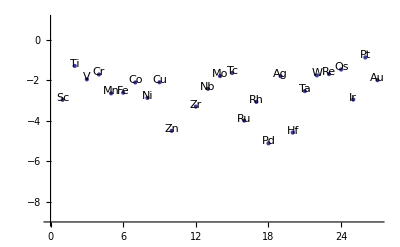

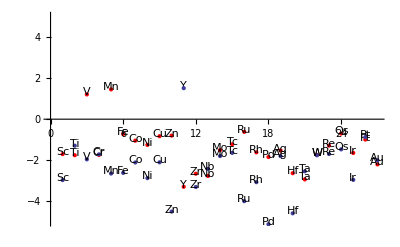

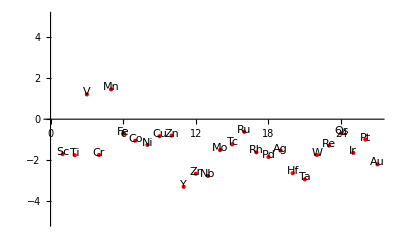

-Graphics-

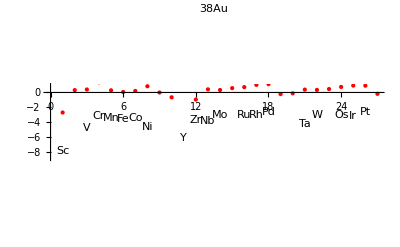

```mathematica
dataPlot1=ListPlot[smallBindingTable[[All,10]] - ORR /. targets,PlotStyle->PointSize->Large,AxesOrigin->{0,-9},PlotRange->{Automatic,{-9,1}}];
labels1=MapThread[Text[#1,{#2,#3+0.1- ORR /. targets}]&,{elements,Range[Length@smallBindingTable[[All,10]]],smallBindingTable[[All,10]]}];
Show[dataPlot1,Graphics[labels1]]

dataPlot2=ListPlot[bigBindingTable[[All,10]] - ORR /. targets,PlotStyle->{Red,PointSize->Large},AxesOrigin->{0,0},PlotRange->{Automatic,{-5,5}}];
labels2=MapThread[Text[#1,{#2,#3+0.1- ORR /. targets}]&,{elements,Range[Length@bigBindingTable[[All,10]]],bigBindingTable[[All,10]]}];

dataPlot3=ListPlot[smallBindingTable[[All,27]] - ORR /. targets,PlotStyle->{Red,PointSize->Large},PlotRange->{Automatic,{-9,1}},PlotLabel -> "38Au", AxesOrigin->{0,0} ];
labels3=MapThread[Text[#1,{#2,#3+0.01- ORR /. targets}]&,{elements,Range[Length@smallBindingTable[[All,10]]],smallBindingTable[[All,5]]}];


Show[dataPlot2,Graphics[labels2], dataPlot1, Graphics[labels1]]
Show[dataPlot2,Graphics[labels2]]
Show[dataPlot1, Graphics[labels1]]
Show[dataPlot3,Graphics[labels3]]
```

## Average Bond Length Plots:

```mathematica
bondLenData = Import["/home/marco/fridbDemo/avgbondlen.json"] /. elementList;
```

Get Bond Length for bnp 38 nanoparticles

```mathematica
lst=  "bnp" /. bondLenData[[1]];
lst = "38" /. lst;

lst = Delete[lst,3];
lst = Delete[lst,8];
bnp38BL = Table[x, {x,1,27}] /. lst;
```

Get Bond Length for bnp 79 nanoparticles:

```mathematica
lst2=  "bnp" /. bondLenData[[1]];
lst2 = "79" /. lst2;
lst2 = Delete[lst,3];
lst2 = Delete[lst,8];
bnp79BL = Table[x, {x,1,27}] /. lst2; 

bondLenData[[1]]
```

bnp→{38→{19→2.85077,27→2.8549,Cd→2.88438,7→2.8297,4→2.84034,9→2.81286,6→2.8282,20→2.96446,Hg→2.87532,25→2.83727,5→2.83799,14→2.84114,13→2.91995,8→2.83038,24→2.84655,18→2.84554,26→2.84533,23→2.86048,17→2.84004,16→2.84042,1→2.92212,21→2.91318,15→2.85081,2→2.88824,3→2.87623,22→2.89723,11→2.96313,10→2.84196,12→2.97649},79→{19→2.87259,27→2.87463,Cd→2.88172,7→2.78466,4→2.82841,9→2.80938,6→2.77798,20→3.00874,25→2.81191,5→2.80125,14→2.82716,13→2.83941,8→2.7879,24→2.79815,18→2.82765,26→2.83002,23→2.8378,17→2.81816,16→2.80325,1→2.9742,21→2.96703,15→2.82528,2→2.8858,3→2.80727,22→2.83959,11→2.96012,10→2.85065}}

Make Plots of Bond Length data:

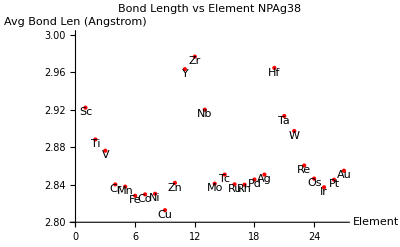

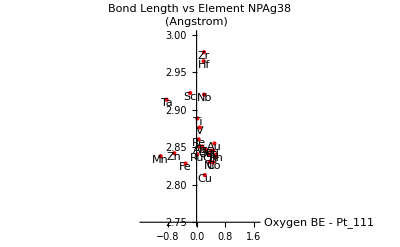

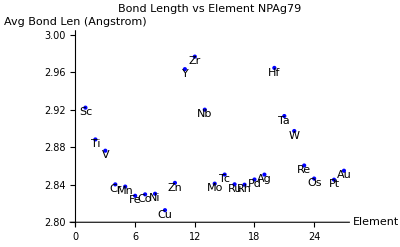

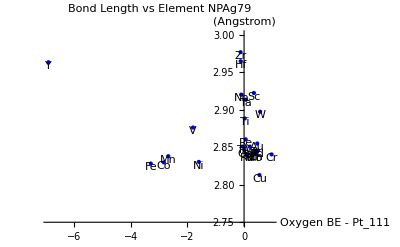

```mathematica
bondLenVsElement38 = ListPlot[bnp38BL, PlotStyle -> {Red, PointSize -> Large},PlotRange -> {2.80, 3},  PlotLabel -> "Bond Length vs Element NPAg38", AxesLabel->{"Element", "Avg Bond Len (Angstrom)"}];
bondLenVsElementLabels38=MapThread[Text[#1,{#2,#3-0.005}]&,{elements,Range[Length@bnp38BL], bnp38BL}];

bondLenVsBe38data = Partition[#,2] & @Riffle[#1, #2] & @@{smallBindingTable[[All,19]] - ORR /. targets, bnp38BL};
bondLenVsBe38=ListPlot[bondLenVsBe38data, PlotStyle->{Red,PointSize->Large}, PlotRange->{2.75, 3}, PlotLabel -> "Bond Length vs Element NPAg38", AxesLabel->{"Oxygen BE - Pt_111", "(Angstrom)"}];
bondLenVsBeLabels38=MapThread[Text[#1,{#2 ,#3- 0.005}]&,{elements,smallBindingTable[[All,19]] - ORR /. targets, bnp38BL}];

bondLenVsElement79 = ListPlot[bnp79BL, PlotStyle -> {Blue, PointSize -> Large},PlotRange -> {2.80, 3},  PlotLabel -> "Bond Length vs Element NPAg79", AxesLabel->{"Element", "Avg Bond Len (Angstrom)"}];
bondLenVsElementLabels79=MapThread[Text[#1,{#2,#3-0.005}]&,{elements,Range[Length@bnp79BL], bnp79BL}];

bondLenVsBe79data = Partition[#,2] & @Riffle[#1, #2] & @@{bigBindingTable[[All,19]] - ORR /. targets, bnp79BL};
bondLenVsBe79=ListPlot[bondLenVsBe79data, PlotStyle->{Blue,PointSize->Large}, PlotRange->{2.75, 3}, PlotLabel -> "Bond Length vs Element NPAg79", AxesLabel->{"Oxygen BE - Pt_111", "(Angstrom)"}];
bondLenVsBeLabels79=MapThread[Text[#1,{#2 ,#3- 0.005}]&,{elements,bigBindingTable[[All,19]] - ORR /. targets, bnp79BL}];




Show[bondLenVsElement38, Graphics[bondLenVsElementLabels38] ]
Show[bondLenVsBe38, Graphics[bondLenVsBeLabels38] ]

Show[bondLenVsElement79, Graphics[bondLenVsElementLabels79] ]
Show[bondLenVsBe79, Graphics[bondLenVsBeLabels79] ]
```

## Filter Particles:

```mathematica
assignNums[sege_] :=If[ sege[[1]] == 0 && sege[[2]] == 0, 3, 
If[ sege[[1]] > 0 && sege[[2]] > 0, 1, 
If[ Xor[sege[[1]] ≥ 0, sege[[2]] ≥ 0], 2,
If[ sege[[1]] ≤ 0 &&  sege[[2]] ≤ 0, -1

]
]
]
] 
  
segColor = {2->Yellow, 1 -> Green, -1 -> Red, 3 -> Black};

getSmallSeg[core_,shell_] :=If[core == shell, {0,0},{smallSegTable[[core, shell ]] , smallSegTableOxygen[[core, shell]]}]
getBigSeg[core_,shell_] :=If[core == shell, {0,0},{bigSegTable[[core, shell ]] , bigSegTableOxygen[[core, shell]]}]

joinNames[el1_, el2_] := Table[el1[[i]]<>"@"<>el2[[i]], {i, Length[el1]}]

selIdealCol[myLst_, element_] :=Cases[idealOrrBigDisp,{txt_, core_,shell_,ΔE_}/;shell == element]
```

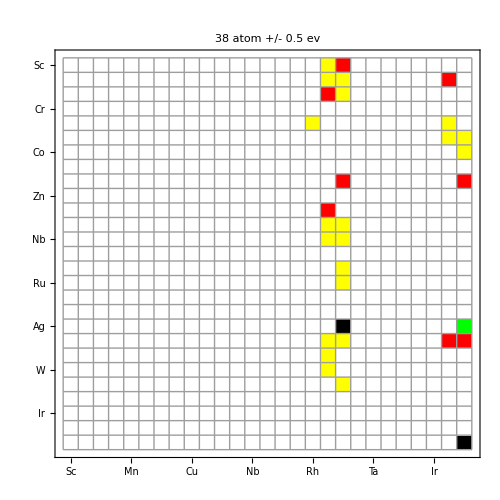

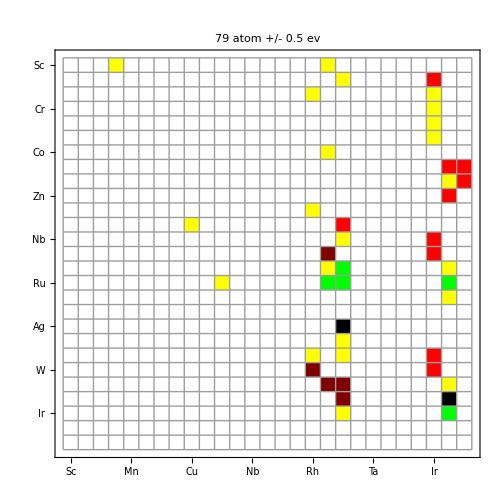

```mathematica
idealORRSmall = Replace[smallBindingTable- (ORR) /. targets,a_/;Abs[a]≥0.25->0,{2}] ;
idealORRBig = Replace[bigBindingTable- (ORR) /. targets ,a_/;Abs[a] ≥  0.25->0,{2}];


info[tbl_]:=With[{s=SparseArray[tbl]},ArrayPad[Append@@@Transpose[{s["NonzeroPositions"],s["NonzeroValues"]}],{0,{1,0}},ToString@Unevaluated@tbl]];

SetAttributes[info,HoldFirst];


idealOrrSmallDisp = DeleteCases[  info[idealORRSmall]/.  Reverse /@ elementList,{__,"no"}];
idealOrrBigDisp = DeleteCases[  info[idealORRBig]/.  Reverse /@ elementList,{__,"no"}];

idealSmallPairs = {#2, #3} & @@@ DeleteCases[  info[idealORRSmall]/. elementList,{__,"no"}];
idealSmallSeglst =assignNums[getSmallSeg[#1,#2]]& @@@ idealSmallPairs;

idealBigPairs = {#2, #3} & @@@ DeleteCases[  info[idealORRBig]/.elementList,{__,"no"}];
idealBigSeglst =assignNums[getBigSeg[#1,#2]]& @@@ idealBigPairs;

myDataIdealSmallSeglst = Table[Insert[idealSmallPairs[[i]],idealSmallSeglst[[i]],3],{i,Length[idealSmallSeglst] }];
myDataIdealBigSeglst = Table[Insert[idealBigPairs[[i]],idealBigSeglst[[i]],3],{i,Length[idealBigSeglst] }];

MatrixPlot[ SparseArray[ # ->  myDataIdealSmallSeglst[[All,3]], {27,27} ] & @ idealSmallPairs,ColorRules-> segColor,Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500, PlotLabel->"38 atom +/- 0.5 ev"]

MatrixPlot[ SparseArray[ # ->  myDataIdealBigSeglst[[All,3]], {27, 27} ] & @ idealBigPairs,ColorRules-> segColor,Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500,  PlotLabel->"79 atom +/- 0.5 ev"]
```

```mathematica
Flatten[{{},{},{"Ag"},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{"Ag"},{"Ag"},{},{},{},{},{"Ag"},{},{},{},{"Ag"},{},{},{"Ag","Ag"},{"Ag"},{},{"Ag"},{},{},{},{},{"Ag"},{},{"Ag"},{},{"Ag"},{}}]
```

{Ag,Ag,Ag,Ag,Ag,Ag,Ag,Ag,Ag,Ag,Ag,Ag}

#### Graeme’s Suggested Stability Plots

```mathematica
myDataIdealSmallSeglst
```

{{1,18,2},{1,19,-1},{2,18,2},{2,19,2},{2,26,-1},{3,18,-1},{3,19,2},{5,17,2},{5,26,2},{6,26,2},{6,27,2},{7,27,2},{9,19,-1},{9,27,-1},{11,18,-1},{12,18,2},{12,19,2},{13,18,2},{13,19,2},{15,19,2},{16,19,2},{19,19,3},{19,27,1},{20,18,2},{20,19,2},{20,26,-1},{20,27,-1},{21,18,2},{22,18,2},{23,19,2},{27,27,3}}

```mathematica
makeStabilityPlot[pairLst_,segen_, bindingLst_, pltRng_] := Module[{coreShell, labelsBNP,labelsNPO, labelsOverall,  stabilityPlotBNP, stabilityPlotNPO, overAllStability},
coreShell = joinNames[#1, #2] & @@{pairLst[[All,1]], pairLst[[All,2]]}; 
labelsBNP =  MapThread[Text[#1,{#2,#3+0.01}]&,{coreShell,segen[[All,1]],bindingLst}];
labelsNPO =  MapThread[Text[#1,{#2,#3+0.01}]&,{coreShell,segen[[All,2]],bindingLst}];
labelsOverall = MapThread[Text[#1,{#2,#3+0.01}]&,{coreShell,segen[[All,1]],segen[[All,2]]}];

stabilityPlotBNP = ListPlot[Partition[Riffle[segen[[All,1]], bindingLst ], 2],PlotStyle -> { Blue, PointSize->Medium}, AxesLabel-> {"Seg (eV)", "Binding Energy(eV)"}, AxesOrigin -> {0,0}, PlotRange -> pltRng, PlotLabel -> "Stability in vacuum"];
 stabilityPlotNPO =ListPlot[Partition[Riffle[segen[[All,2]], bindingLst ], 2],PlotStyle -> { Red, PointSize->Medium}, AxesLabel-> {"Seg (eV)", "Binding (eV)"}, AxesOrigin->{0,0}, PlotRange -> pltRng, PlotLabel -> "Stability with Oxygen" ];

overAllStability = ListPlot[Partition[Riffle[segen[[All,1]], segen[[All,2]] ], 2],PlotStyle -> { Purple, PointSize->Medium}, AxesLabel-> {"Vac (eV)", "Oxygen Ads. (eV)"}, AxesOrigin->{0,0}, PlotRange -> {pltRng[[1]], pltRng[[1]]}, PlotLabel -> "Overall Stability" ];




 Show[stabilityPlotBNP, Graphics[labelsBNP]]
Show[stabilityPlotNPO, Graphics[labelsNPO]]
Show[overAllStability, Graphics[labelsOverall]]


]



makeStabilityPlot[idealSmallPairs /. Reverse /@ elementList , getSmallSeg[#1,#2]& @@@ idealSmallPairs, idealOrrSmallDisp[[All,4]], {{-5,5}, {-5, 5} } ]
makeStabilityPlot[idealBigPairs /. Reverse /@ elementList, getBigSeg[#1, #2] & @@@ idealBigPairs, idealOrrBigDisp[[All,4]],  {{-1,1}, {-0.6, 0.6} } ]

makeStabilityPlot[  {#2 ,#3 } & @@@selIdealCol[idealOrrBigDisp ,"Ag"], getBigSeg[#1, #2] & @@@ ( ({#2 ,#3 } & @@@selIdealCol[idealOrrBigDisp ,"Ag"]) /. elementList),Flatten[{#4} & @@@selIdealCol[idealOrrBigDisp ,"Ag"]],   {{-2,2},{-0.3,0.3}}]

makeStabilityPlot[  {#2 ,#3 } & @@@selIdealCol[idealOrrBigDisp ,"Pd"], getBigSeg[#1, #2] & @@@ ( ({#2 ,#3 } & @@@selIdealCol[idealOrrBigDisp ,"Pd"]) /. elementList),Flatten[{#4} & @@@selIdealCol[idealOrrBigDisp ,"Pd"]],   {{-2,2},{-0.3,0.3}}]

makeStabilityPlot[  {#2 ,#3 } & @@@selIdealCol[idealOrrBigDisp ,"Rh"], getBigSeg[#1, #2] & @@@ ( ({#2 ,#3 } & @@@selIdealCol[idealOrrBigDisp ,"Rh"]) /. elementList),Flatten[{#4} & @@@selIdealCol[idealOrrBigDisp ,"Rh"]],   {{-2,2},{-0.3,0.3}}]

makeStabilityPlot[  {#2 ,#3 } & @@@selIdealCol[idealOrrBigDisp ,"Ir"], getBigSeg[#1, #2] & @@@ ( ({#2 ,#3 } & @@@selIdealCol[idealOrrBigDisp ,"Ir"]) /. elementList),Flatten[{#4} & @@@selIdealCol[idealOrrBigDisp ,"Ir"]],   {{-2,2},{-0.3,0.3}}]


   

makeStabilityPlot[  {#2 ,#3 } & @@@selIdealCol[idealOrrBigDisp ,"Pt"], getBigSeg[#1, #2] & @@@ ( ({#2 ,#3 } & @@@selIdealCol[idealOrrBigDisp ,"Pt"]) /. elementList),Flatten[{#4} & @@@selIdealCol[idealOrrBigDisp ,"Pt"]],   {{-2,2},{-0.3,0.3}}]
```

### Calculate Correct Ratio for Tuning:

0.38

2.63068 | 2.52168 | 2.74693 | 2.061 | 1.31085
2.77295 | 2.64848 | 2.9067 | 2.13218 | 1.3238
5.60193 | 4.99287 | 6.36177 | 3.14707 | 1.4583

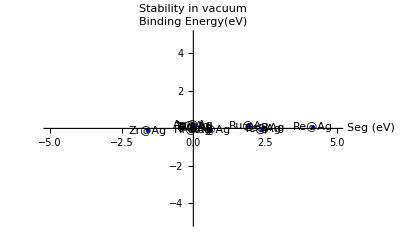
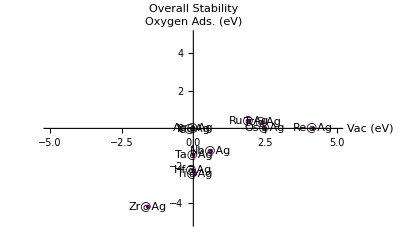
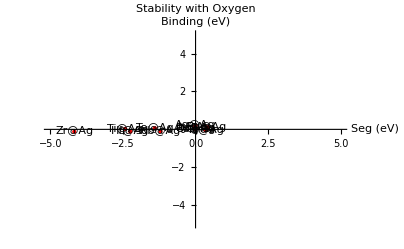

```mathematica
Ylist = {"Au", "Ag", "Pd"};
Xlist = {"Ir", "Rh", "Cu", "Ru", "Mo"};

buildList[inlst_] := Module[{lst1, inLst},

lst1 ={#1, "Rh", bigBindingTable} &  /@inlst /. elementList;
lst1 = returnValue[#1,#2,#3] & @@@ lst1
]
 
computeRatio[in1_, in2_] := (in1 + 1.51)/ (in1 - in2)


(-1.7 + 1.51)/(-1.7 + 1.2)
 Outer[computeRatio, buildList[Ylist], buildList[Xlist]] //TableForm
```

### Filter For Tunable Particles:

```mathematica
returnValueTest[row_, col_,tbl_] := tbl[[row,col]] 
tables = { smallBindingTable, bigBindingTable};
```

#### Filter Small Particles:

```mathematica
returnValue[row_,col_,myTable_]:=myTable[[row,col]];
filter =Replace[smallBindingTable,a_/;Abs[a]≥10->666,{2}]- (-1.51)/.targets; (*set any spurious values to zero *)
(* A particle is tunable if its pure form (located on the diagnols of the table) is opposite in sign to its core@shell parnter *)
d=Sign@Diagonal@filter;

tunablePairs=Position[(filterᵀ d)ᵀ,_?Negative]/.Reverse/@elementList;
pairEnergy=returnValue[#1,#2, smallBindingTable]&@@{#1,#2}&@@@Position[(filterᵀ d)ᵀ,_?Negative];
tempVar=Partition[Riffle[tunablePairs,pairEnergy],2];
filterImposs=Replace[tempVar,a_/;Abs[a]>5->666,{2}];

Cases[filterImposs,{x_,y_}/;x[[2]]≠("Zn")];
Cases[%,{x_,y_}/;x[[2]]≠("Zr")];
Partition[Riffle[ %[[All,1]],%[[All,2]] ],2];
tunableSmall = DeleteCases[%,{x_,y_}/;y==0];

DeleteDuplicates[ Flatten[ tunableSmall[[All,1]] ] ];

pure = Extract[ smallBindingTable, Partition[Riffle[ tunableSmall[[All,1,2]] /. elementList , tunableSmall[[All,1,2]] /. elementList],2]];

(*ratio = idealRatio[finalTunableBig[[All,2]], -1.51, finalTunableBig[[All,3]] ]; *)tunableSmall = ArrayFlatten[{{tunableSmall,Transpose[{pure}]}}];

ratio = (tunableSmall[[All,2]] + 1.51)/(tunableSmall[[All,2]] - tunableSmall[[All,3]]);

finalTunableSmall= ArrayFlatten[{{tunableSmall,Transpose[{ratio}]}}];

finalTunableSmall = DeleteCases[finalTunableSmall,{x_,y_,z_,f_}/;z==666];
finalTunableSmall = DeleteCases[finalTunableSmall,{x_,y_,z_,f_}/;y==666];

Partition[Riffle[finalTunableSmall[[All,1]], finalTunableSmall[[All,4]]],2] ;

finalTunableadj = {#1,#2+1.51,#3+1.51, #4 } &@@@finalTunableSmall[[All,1;;]];
finalTunableadj/. {{l1_,l2_},x1_ ,x2_ ,_}:>Thread@Labeled[Thread@{l2/.elementList,{x1,x2}},{l1,l2}];
SortBy[ finalTunableadj /. elementList,#[[2]]&] /. Reverse /@ elementList;
myPrint[finalTunableadj[[All,1]]]
```

({Sc, Pd} {Sc, Ag} {Ti, Mn} {Ti, Au} {V, Au} {Cr, Cu} {Cr, Au} {Mn, Fe} {Mn, Ag} {Mn, Pt} {Mn, Au} {Fe, Ag} {Fe, Au} {Co, Au} {Ni, Cu} {Ni, Au} {Zn, Ag} {Y, W} {Y, Re} {Y, Au} {Nb, Au} {Mo, Au} {Tc, Mn} {Tc, Au} {Ru, Au} {Rh, Au} {Pd, Fe} {Pd, Mo} {Pd, Au} {Ag, Ir} {Hf, Mn} {Ta, Ag} {Ta, Au} {W, Ir} {W, Au} {Re, Mn} {Re, Fe} {Re, Pt} {Re, Au} {Os, Ti} {Os, Ir} {Os, Au} {Ir, Au} {Pt, Ti} {Pt, Au} {Au, Cu} {Au, Mo} {Au, Ir})

#### Function to get both Segregation energies for particles

### Matrix Plot for Tunable Small

{{1,18},{1,19},{2,5},{2,27},{3,27},{4,9},{4,27},{5,6},{5,19},{5,26},{5,27},{6,19},{6,27},{7,27},{8,9},{8,27},{10,19},{11,22},{11,23},{11,27},{13,27},{14,27},{15,5},{15,27},{16,27},{17,27},{18,6},{18,14},{18,27},{19,25},{20,5},{21,19},{21,27},{22,25},{22,27},{23,5},{23,6},{23,26},{23,27},{24,2},{24,25},{24,27},{25,27},{26,2},{26,27},{27,9},{27,14},{27,25}}

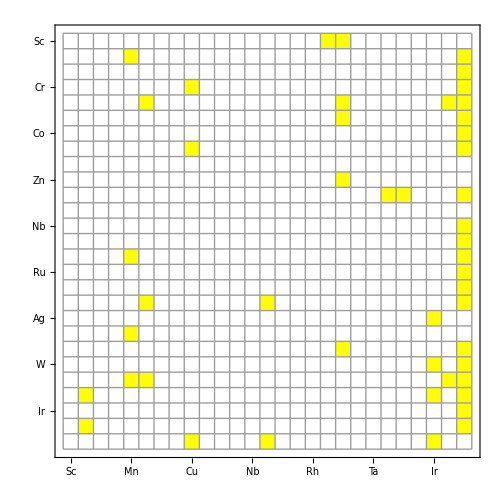

{2,-1,-1,-1,2,2,2,2,1,2,2,2,2,2,2,-1,-1,-1,2,2,2,-1,1,2,2,2,-1,-1,2,-1,2,2,2,2,2,1,2,2,2,-1,2,2,2,-1,1,-1,2,-1}

{{1,18,2},{1,19,-1},{2,5,-1},{2,27,-1},{3,27,2},{4,9,2},{4,27,2},{5,6,2},{5,19,1},{5,26,2},{5,27,2},{6,19,2},{6,27,2},{7,27,2},{8,9,2},{8,27,-1},{10,19,-1},{11,22,-1},{11,23,2},{11,27,2},{13,27,2},{14,27,-1},{15,5,1},{15,27,2},{16,27,2},{17,27,2},{18,6,-1},{18,14,-1},{18,27,2},{19,25,-1},{20,5,2},{21,19,2},{21,27,2},{22,25,2},{22,27,2},{23,5,1},{23,6,2},{23,26,2},{23,27,2},{24,2,-1},{24,25,2},{24,27,2},{25,27,2},{26,2,-1},{26,27,1},{27,9,-1},{27,14,2},{27,25,-1}}

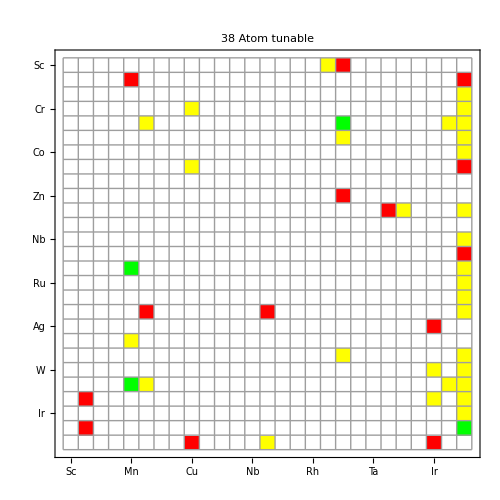

```mathematica
smallPairs = finalTunableadj[[All,1]] /.elementList
finalTunableadj[[All,1]] >> small.txt 
MatrixPlot[ SparseArray[ # -> 1, {27,27}] & @ smallPairs,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]



SmallSeglst = assignNums[getSmallSeg[#1,#2]]& @@@ smallPairs

myDataSmallSeglst = Table[Insert[smallPairs[[i]],SmallSeglst[[i]],3],{i,Length[SmallSeglst] }]



MatrixPlot[ SparseArray[ # ->  myDataSmallSeglst[[All,3]], {27,27} ] & @ smallPairs,ColorRules-> segColor,Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500, PlotLabel->"38 Atom tunable"]
```

#### Filter Large:

```mathematica
returnValue[row_,col_,myTable_]:=myTable[[row,col]];
filter =Replace[bigBindingTable,a_/;Abs[a]≥10->666,{2}]- (-1.51)/.targets; (*set any spurious values to zero *)
(* A particle is tunable if its pure form (located on the diagnols of the table) is opposite in sign to its core@shell parnter *)

d=Sign@Diagonal@filter;

tunablePairs=Position[(filterᵀ d)ᵀ,_?Negative]/.Reverse/@elementList;
pairEnergy=returnValue[#1,#2, bigBindingTable]&@@{#1,#2}&@@@Position[(filterᵀ d)ᵀ,_?Negative];
tempVar=Partition[Riffle[tunablePairs,pairEnergy],2];
filterImposs=Replace[tempVar,a_/;Abs[a]>5->666,{2}];

Cases[filterImposs,{x_,y_}/;x[[2]]≠("Zn")];
Cases[%,{x_,y_}/;x[[2]]≠("Zr")];
Partition[Riffle[ %[[All,1]],%[[All,2]] ],2];
tunableBig = DeleteCases[%,{x_,y_}/;y==0];


 DeleteDuplicates[ Flatten[ tunableBig[[All,1]] ] ];

pure = Extract[ bigBindingTable, Partition[Riffle[ tunableBig[[All,1,2]] /. elementList , tunableBig[[All,1,2]] /. elementList],2]];

(*ratio = idealRatio[finalTunableBig[[All,2]], -1.51, finalTunableBig[[All,3]] ]; *)
tunableBig = ArrayFlatten[{{tunableBig,Transpose[{pure}]}}];

ratio = (tunableBig[[All,2]] + 1.51)/(tunableBig[[All,2]] - tunableBig[[All,3]]);

finalTunableBig= ArrayFlatten[{{tunableBig,Transpose[{ratio}]}}];
finalTunableBig = DeleteCases[finalTunableBig,{x_,y_,z_,f_}/;z==666];
finalTunableBig = DeleteCases[finalTunableBig,{x_,y_,z_,f_}/;y==666];

Partition[Riffle[finalTunableBig[[All,1]], finalTunableBig[[All,4]]],2] 

finalTunableadj = {#1,#2+1.51,#3+1.51, #4 } &@@@finalTunableBig[[All,1;;]];

finalTunableadj/. {{l1_,l2_},x1_ ,x2_ ,_}:>Thread@Labeled[Thread@{l2/.elementList,{x1,x2}},{l1,l2}];

SortBy[ finalTunableadj /. elementList,#[[2]]&] /. Reverse /@ elementList;
myPrint[finalTunableadj[[All,1]]]

finalTunableBig
```

{{{Sc,Cr},0.0266889},{{Sc,Tc},0.161776},{{Ti,Pd},0.472351},{{Ti,Pt},0.642577},{{V,Pd},0.453805},{{V,Ag},0.901294},{{V,Ir},0.184013},{{V,Au},0.291374},{{Cr,Y},0.184363},{{Cr,Pt},0.523214},{{Mn,Ag},0.931177},{{Mn,Ir},0.0333165},{{Mn,Au},0.701385},{{Fe,Ag},0.943395},{{Fe,Hf},0.0458067},{{Fe,Au},0.755131},{{Co,Sc},0.00392582},{{Co,Ag},0.934762},{{Co,Au},0.675431},{{Ni,Ag},0.889929},{{Ni,Pt},0.278007},{{Ni,Au},0.18592},{{Cu,Cr},0.0736894},{{Cu,Hf},0.11091},{{Cu,Pt},0.112997},{{Zn,Sc},0.0212429},{{Zn,Mn},0.125739},{{Zn,Pd},0.355474},{{Y,Mn},0.221391},{{Y,Rh},0.0536183},{{Y,Pt},0.731322},{{Y,Au},0.541199},{{Zr,Pd},0.414845},{{Zr,Ag},0.382869},{{Nb,Pd},0.289726},{{Nb,Ag},0.344795},{{Nb,Pt},0.485101},{{Mo,Y},0.149937},{{Mo,Pd},0.274933},{{Tc,Pd},0.21032},{{Tc,Ag},0.189142},{{Tc,Pt},0.264183},{{Ru,Y},0.0266547},{{Ru,Pt},0.138439},{{Hf,Pd},0.448315},{{Hf,Ag},0.378757},{{Hf,Au},0.766731},{{Ta,Pd},0.405936},{{Ta,Ir},0.0621974},{{Ta,Pt},0.458816},{{Ta,Au},0.718747},{{W,Rh},0.0626802},{{W,Pd},0.394706},{{W,Pt},0.371036},{{Re,Pt},0.0286588},{{Os,Pt},0.0510915},{{Ir,Y},0.264562}}

({Sc, Cr} {Sc, Tc} {Ti, Pd} {Ti, Pt} {V, Pd} {V, Ag} {V, Ir} {V, Au} {Cr, Y} {Cr, Pt} {Mn, Ag} {Mn, Ir} {Mn, Au} {Fe, Ag} {Fe, Hf} {Fe, Au} {Co, Sc} {Co, Ag} {Co, Au} {Ni, Ag} {Ni, Pt} {Ni, Au} {Cu, Cr} {Cu, Hf} {Cu, Pt} {Zn, Sc} {Zn, Mn} {Zn, Pd} {Y, Mn} {Y, Rh} {Y, Pt} {Y, Au} {Zr, Pd} {Zr, Ag} {Nb, Pd} {Nb, Ag} {Nb, Pt} {Mo, Y} {Mo, Pd} {Tc, Pd} {Tc, Ag} {Tc, Pt} {Ru, Y} {Ru, Pt} {Hf, Pd} {Hf, Ag} {Hf, Au} {Ta, Pd} {Ta, Ir} {Ta, Pt} {Ta, Au} {W, Rh} {W, Pd} {W, Pt} {Re, Pt} {Os, Pt} {Ir, Y})

{{{Sc,Cr},-1.38635,-6.01922,0.0266889},{{Sc,Tc},-1.04173,-3.93627,0.161776},{{Ti,Pd},-0.944052,-2.1422,0.472351},{{Ti,Pt},-0.458595,-2.09483,0.642577},{{V,Pd},-0.984736,-2.1422,0.453805},{{V,Ag},-3.31205,-1.31265,0.901294},{{V,Ir},-1.3077,-2.4071,0.184013},{{V,Au},-1.80741,-0.786697,0.291374},{{Cr,Y},-0.396658,-6.43553,0.184363},{{Cr,Pt},-0.868226,-2.09483,0.523214},{{Mn,Ag},-4.18021,-1.31265,0.931177},{{Mn,Ir},-1.47908,-2.4071,0.0333165},{{Mn,Au},-3.20889,-0.786697,0.701385},{{Fe,Ag},-4.79914,-1.31265,0.943395},{{Fe,Hf},-1.25885,-6.74177,0.0458067},{{Fe,Au},-3.74054,-0.786697,0.755131},{{Co,Sc},-2.13313,156.593,0.00392582},{{Co,Ag},-4.3378,-1.31265,0.934762},{{Co,Au},-3.0152,-0.786697,0.675431},{{Ni,Ag},-3.10561,-1.31265,0.889929},{{Ni,Pt},-1.28481,-2.09483,0.278007},{{Ni,Au},-1.67519,-0.786697,0.18592},{{Cu,Cr},-1.15129,-6.01922,0.0736894},{{Cu,Hf},-0.857359,-6.74177,0.11091},{{Cu,Pt},-1.4355,-2.09483,0.112997},{{Zn,Sc},-4.94146,156.593,0.0212429},{{Zn,Mn},-1.08701,-4.45107,0.125739},{{Zn,Pd},-1.16132,-2.1422,0.355474},{{Y,Mn},-0.673729,-4.45107,0.221391},{{Y,Rh},-1.43653,-2.80686,0.0536183},{{Y,Pt},0.081853,-2.09483,0.731322},{{Y,Au},-2.36321,-0.786697,0.541199},{{Zr,Pd},-1.0618,-2.1422,0.414845},{{Zr,Ag},-1.63244,-1.31265,0.382869},{{Nb,Pd},-1.25212,-2.1422,0.289726},{{Nb,Ag},-1.61386,-1.31265,0.344795},{{Nb,Pt},-0.959019,-2.09483,0.485101},{{Mo,Y},-0.641215,-6.43553,0.149937},{{Mo,Pd},-1.27028,-2.1422,0.274933},{{Tc,Pd},-1.34162,-2.1422,0.21032},{{Tc,Ag},-1.55604,-1.31265,0.189142},{{Tc,Pt},-1.30003,-2.09483,0.264183},{{Ru,Y},-1.37512,-6.43553,0.0266547},{{Ru,Pt},-1.41603,-2.09483,0.138439},{{Hf,Pd},-0.996253,-2.1422,0.448315},{{Hf,Ag},-1.63032,-1.31265,0.378757},{{Hf,Au},-3.88743,-0.786697,0.766731},{{Ta,Pd},-1.078,-2.1422,0.405936},{{Ta,Ir},-1.4505,-2.4071,0.0621974},{{Ta,Pt},-1.01418,-2.09483,0.458816},{{Ta,Au},-3.35841,-0.786697,0.718747},{{W,Rh},-1.42328,-2.80686,0.0626802},{{W,Pd},-1.09775,-2.1422,0.394706},{{W,Pt},-1.165,-2.09483,0.371036},{{Re,Pt},-1.49275,-2.09483,0.0286588},{{Os,Pt},-1.47851,-2.09483,0.0510915},{{Ir,Y},0.261878,-6.43553,0.264562}}

### Matrix Plot Tunable Large:

{{1,4},{1,15},{2,18},{2,26},{3,18},{3,19},{3,25},{3,27},{4,11},{4,26},{5,19},{5,25},{5,27},{6,19},{6,20},{6,27},{7,1},{7,19},{7,27},{8,19},{8,26},{8,27},{9,4},{9,20},{9,26},{10,1},{10,5},{10,18},{11,5},{11,17},{11,26},{11,27},{12,18},{12,19},{13,18},{13,19},{13,26},{14,11},{14,18},{15,18},{15,19},{15,26},{16,11},{16,26},{20,18},{20,19},{20,27},{21,18},{21,25},{21,26},{21,27},{22,17},{22,18},{22,26},{23,26},{24,26},{25,11}}

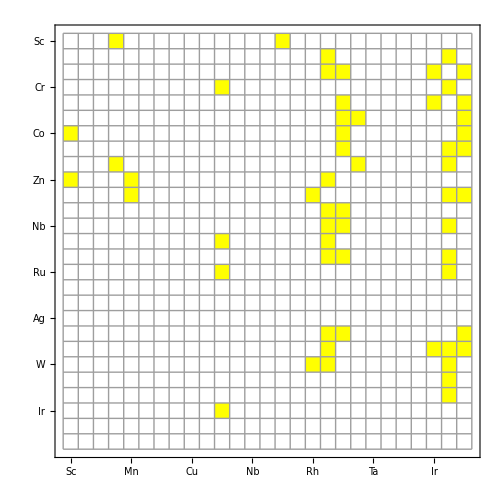

{2,2,2,-1,-1,-1,2,-1,Null,2,2,2,-1,-1,2,-1,2,-1,-1,-1,-1,-1,Null,1,2,2,1,-1,-1,2,-1,1,2,-1,2,2,2,3,Null,2,1,2,2,1,-1,2,-1,Null,-1,2,-1,Null,2,-1,2,3,2}

{{1,4,2},{1,15,2},{2,18,2},{2,26,-1},{3,18,-1},{3,19,-1},{3,25,2},{3,27,-1},{4,11,Null},{4,26,2},{5,19,2},{5,25,2},{5,27,-1},{6,19,-1},{6,20,2},{6,27,-1},{7,1,2},{7,19,-1},{7,27,-1},{8,19,-1},{8,26,-1},{8,27,-1},{9,4,Null},{9,20,1},{9,26,2},{10,1,2},{10,5,1},{10,18,-1},{11,5,-1},{11,17,2},{11,26,-1},{11,27,1},{12,18,2},{12,19,-1},{13,18,2},{13,19,2},{13,26,2},{14,11,3},{14,18,Null},{15,18,2},{15,19,1},{15,26,2},{16,11,2},{16,26,1},{20,18,-1},{20,19,2},{20,27,-1},{21,18,Null},{21,25,-1},{21,26,2},{21,27,-1},{22,17,Null},{22,18,2},{22,26,-1},{23,26,2},{24,26,3},{25,11,2}}

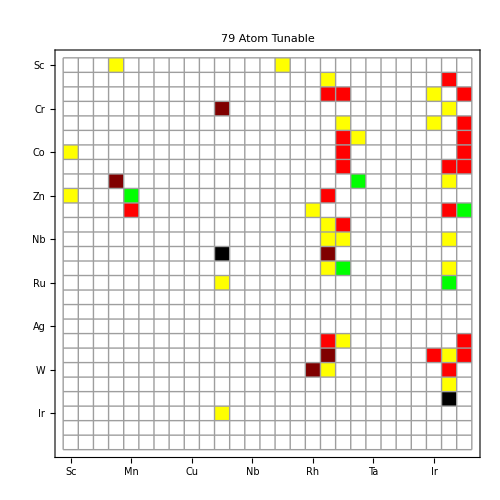

```mathematica
bigPairs = finalTunableadj[[All,1]] /.elementList
MatrixPlot[ SparseArray[ # -> 1, {27,27}] & @ bigPairs,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]



BigSeglst = assignNums[getBigSeg[#1,#2]]& @@@ bigPairs

myDataBigSeglst = Table[Insert[bigPairs[[i]],BigSeglst[[i]],3],{i,Length[BigSeglst] }]



MatrixPlot[ SparseArray[ # -> myDataBigSeglst[[All,3]], {27, 27} ] & @ bigPairs,ColorRules-> segColor,Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500, PlotLabel->"79 Atom Tunable"]
```

### Stability Plots for Tunable Particles:

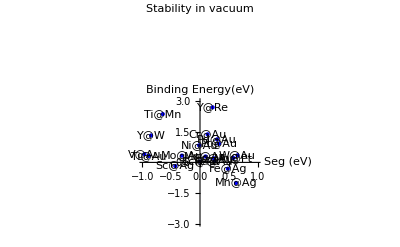
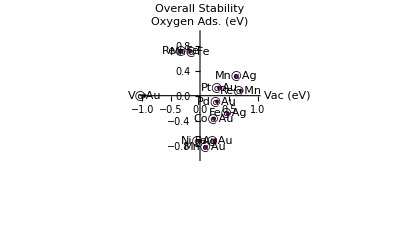
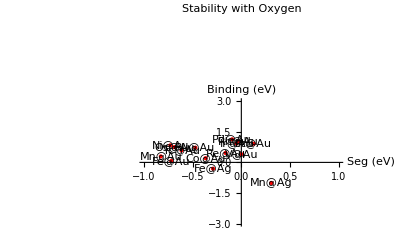

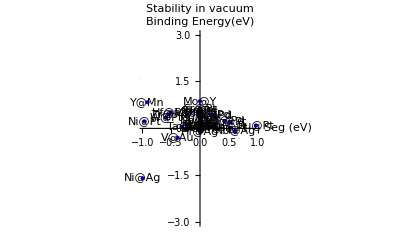
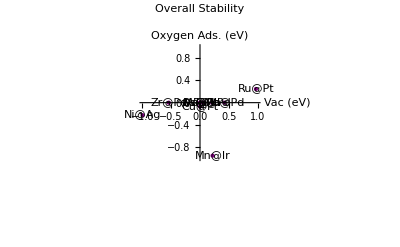
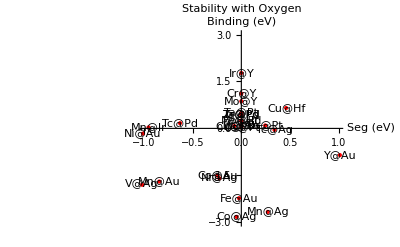

```mathematica
makeStabilityPlot[smallPairs /. Reverse /@ elementList , getSmallSeg[#1,#2]& @@@ smallPairs, finalTunableSmall[[All,2]] - ORR /. targets, {{-1,1}, {-3, 3} } ]

makeStabilityPlot[bigPairs /. Reverse /@ elementList , getBigSeg[#1,#2]& @@@ bigPairs, finalTunableBig[[All,2]] - ORR /. targets, {{-1,1}, {-3, 3} } ]
```

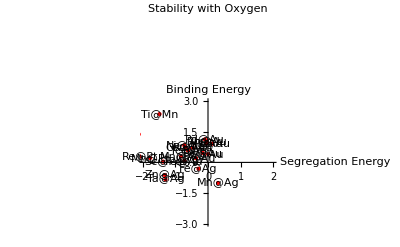
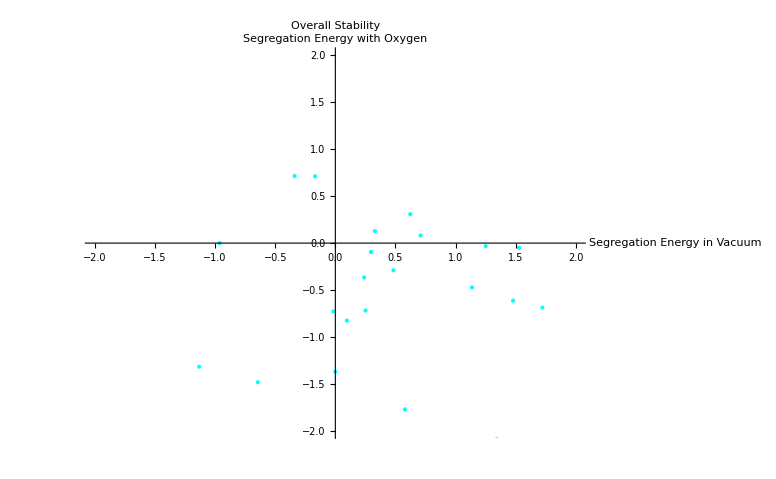

-Graphics- -Graphics-

#### Format Data Table for export:

```mathematica
core = PrependTo[finalTunableadj[[All,1,1]], "  "];
finaltunableadja
```

finaltunableadja

## Final Figures:

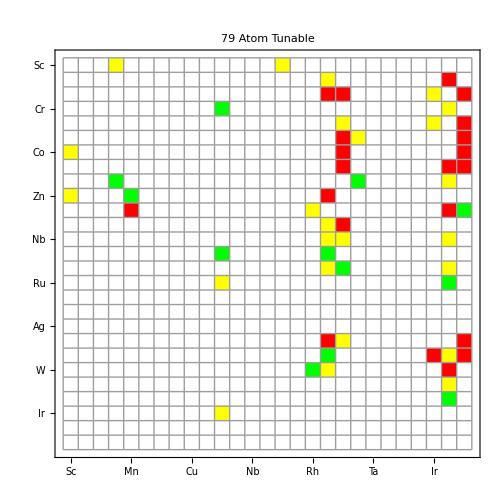
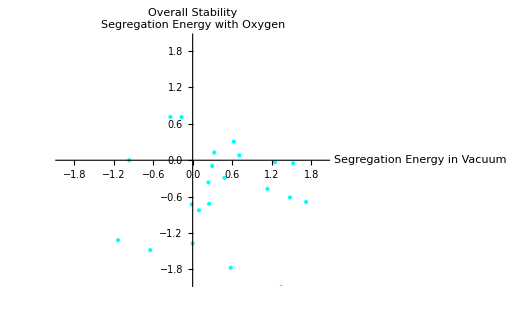
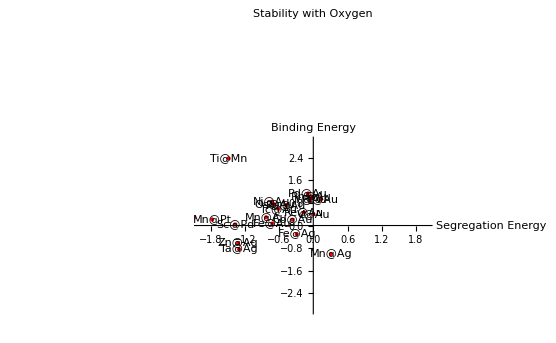
```mathematica
-Graphics--Graphics-
-Graphics-
 -Graphics-
```

-Graphics- -Graphics-

-Graphics-

-Graphics-

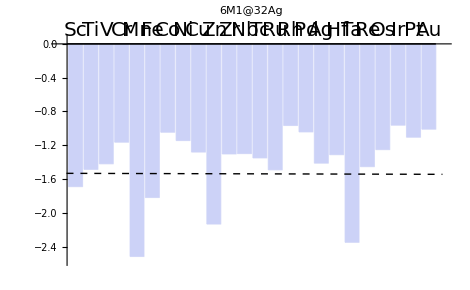
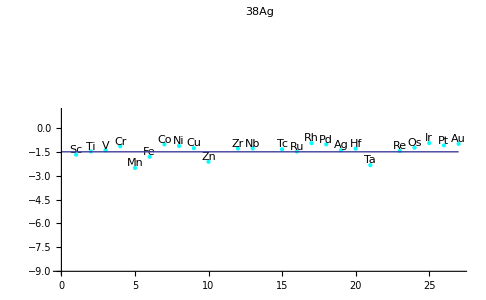
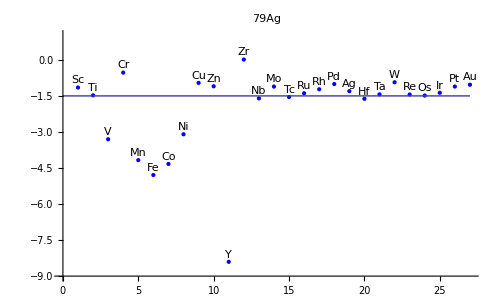
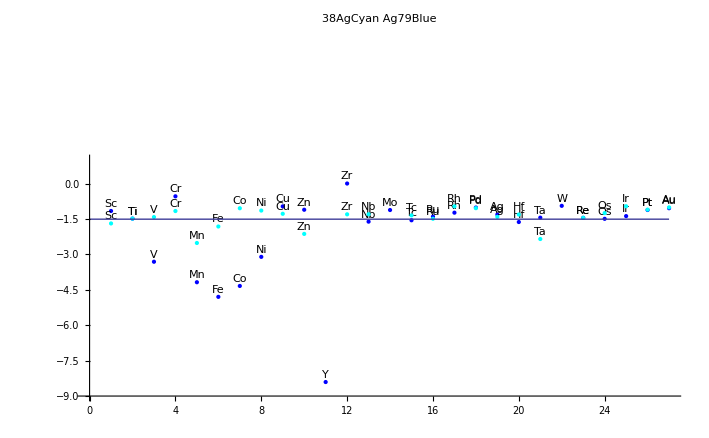
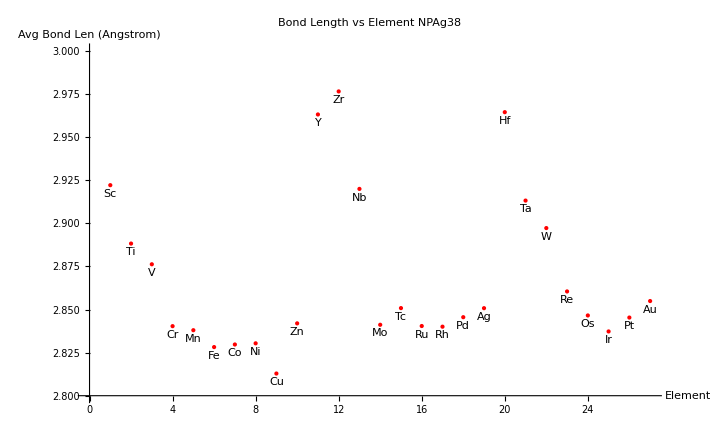
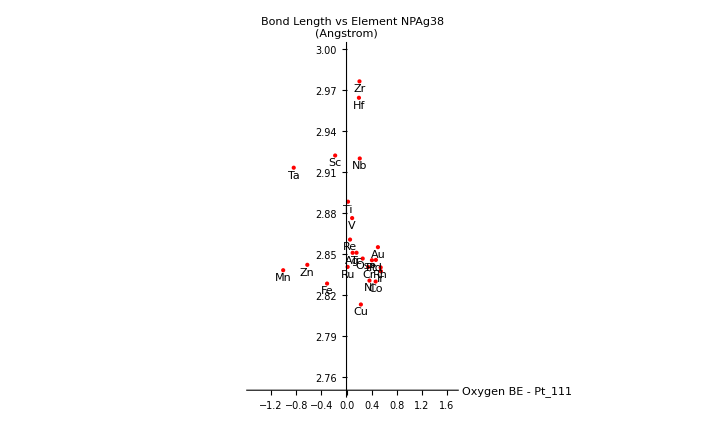
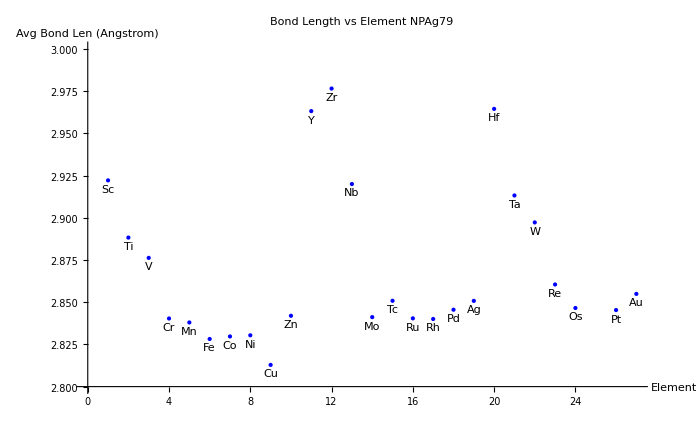
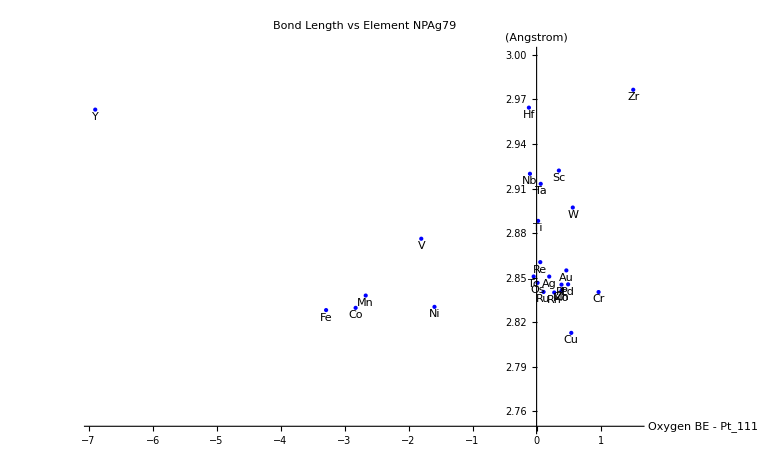
```mathematica
Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics-
```

Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics-

```mathematica
Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics-
```

Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics-

```mathematica
stackTest = {{1,2,3,4,5,6,7,8,9,10}}
```

{{1,2,3,4,5,6,7,8,9,10}}

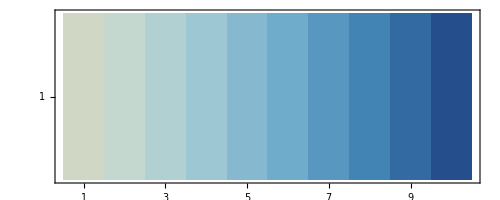

```mathematica
MatrixPlot[stackTest, ColorFunction->"RedBlueTones"]
```

```mathematica
Length[tunableORRData]
```

27

```mathematica
smallBindingTable
```

```mathematica
Function[myTable, {tunableORRData = Replace[myTable ,a_/;Abs[a]≥10->0,{2}] - ORR /. targets;d=Sign@Diagonal@tunableORRData; returnValue[row_, col_,myTable] := myTable[[row,col]] ;tunablePairs = Position[(tunableORRDataᵀ d)ᵀ,_?Negative]  /. Reverse /@ elementList; pairEnergy = returnValue[#1, #2]& @@{#1,#2}&@@@Position[(tunableORRDataᵀ d)ᵀ,_?Negative] ;
tempVar = Partition[Riffle[tunablePairs, pairEnergy],2];
filterImposs = Replace[tempVar,a_/;Abs[a]≥5->0 ,{2}] ;
filterImposs = Replace[filterImposs,a_/;a > 1->0 ,{2}] ;
Cases[filterImposs,{x_,y_}/;y ≠ 0]}][#] & /@ {smallBindingTable, bigBindingTable}








(*Cases[tt,x_/;Abs[x[[1]]-x[[2]]]>3];*)
```

```mathematica
tst = { {1,2,3}, {2,3,4}, {4,5,6} }
```

{{1,2,3},{2,3,4},{4,5,6}}

```mathematica
tst[[All,1]]
tst[[All,2]]
```

{1,2,4}

{2,3,5}

```mathematica
{2,3,5}
```

{2,3,5}

```mathematica
L[#]& @@{1}
```

L[1]

```mathematica
shit = { { {a,b},1,2 }, { {l,x},2,5 } }
```

{{{{{1,18},{1,19},{2,5},{2,27},{3,27},{4,9},{4,27},{5,6},{5,19},{5,26},{5,27},{6,19},{6,27},{7,27},{8,9},{8,27},{10,19},{11,22},{11,23},{11,27},{13,27},{14,27},{15,5},{15,27},{16,27},{17,27},{18,6},{18,14},{18,27},{19,25},{20,5},{21,19},{21,27},{22,25},{22,27},{23,5},{23,6},{23,26},{23,27},{24,2},{24,25},{24,27},{25,27},{26,2},{26,27},{27,9},{27,14},{27,25}},b},1,2},{{l,x},2,5}}

```mathematica
Thread[Append, shit ,{2}]
```

Append

```mathematica
m[[1]]
```

Part::partd: Part specification m ⟦ 1 ⟧ is longer than depth of object.

m⟦1⟧

```mathematica
bigSegTableOxygen⟦1,1⟧
```

0.00165928

```mathematica
a = {{1,18},{1,19},{2,5},{2,27},{3,27},{4,9},{4,27},{5,6},{5,19},{5,26},{5,27},{6,19},{6,27},{7,27},{8,9},{8,27},{10,19},{11,22},{11,23},{11,27},{13,27},{14,27},{15,5},{15,27},{16,27},{17,27},{18,6},{18,14},{18,27},{19,25},{20,5},{21,19},{21,27},{22,25},{22,27},{23,5},{23,6},{23,26},{23,27},{24,2},{24,25},{24,27},{25,27},{26,2},{26,27},{27,9},{27,14},{27,25}}
```

{{1,18},{1,19},{2,5},{2,27},{3,27},{4,9},{4,27},{5,6},{5,19},{5,26},{5,27},{6,19},{6,27},{7,27},{8,9},{8,27},{10,19},{11,22},{11,23},{11,27},{13,27},{14,27},{15,5},{15,27},{16,27},{17,27},{18,6},{18,14},{18,27},{19,25},{20,5},{21,19},{21,27},{22,25},{22,27},{23,5},{23,6},{23,26},{23,27},{24,2},{24,25},{24,27},{25,27},{26,2},{26,27},{27,9},{27,14},{27,25}}

```mathematica
mylst = assignNums[getBigSeg[#1,#2]]& @@@ a

Table[Insert[a[[i]],mylst[[i]],3],{i,Length[mylst] }]
```

{2,2,-1,2,-1,1,2,2,2,-1,-1,-1,-1,-1,2,-1,-1,-1,3,1,-1,2,-1,2,1,2,Null,2,2,-1,2,2,-1,-1,Null,2,-1,2,Null,1,2,1,2,-1,2,2,2,2}

{{1,18,2},{1,19,2},{2,5,-1},{2,27,2},{3,27,-1},{4,9,1},{4,27,2},{5,6,2},{5,19,2},{5,26,-1},{5,27,-1},{6,19,-1},{6,27,-1},{7,27,-1},{8,9,2},{8,27,-1},{10,19,-1},{11,22,-1},{11,23,3},{11,27,1},{13,27,-1},{14,27,2},{15,5,-1},{15,27,2},{16,27,1},{17,27,2},{18,6,Null},{18,14,2},{18,27,2},{19,25,-1},{20,5,2},{21,19,2},{21,27,-1},{22,25,-1},{22,27,Null},{23,5,2},{23,6,-1},{23,26,2},{23,27,Null},{24,2,1},{24,25,2},{24,27,1},{25,27,2},{26,2,-1},{26,27,2},{27,9,2},{27,14,2},{27,25,2}}

```mathematica
idealBigPairs /. Reverse/@ elementList

x /. x -> 2

elementList
```

{{Sc,Cr},{Sc,Pd},{Ti,Ag},{Ti,Ir},{V,Rh},{V,Ir},{Cr,Ir},{Mn,Ir},{Fe,Ir},{Co,Pd},{Ni,Pt},{Ni,Au},{Cu,Pt},{Cu,Au},{Zn,Pt},{Y,Rh},{Zr,Cu},{Zr,Ag},{Nb,Ag},{Nb,Ir},{Mo,Pd},{Mo,Ir},{Tc,Pd},{Tc,Ag},{Tc,Pt},{Ru,Y},{Ru,Pd},{Ru,Ag},{Ru,Pt},{Rh,Pt},{Ag,Ag},{Hf,Ag},{Ta,Rh},{Ta,Ag},{Ta,Ir},{W,Rh},{W,Ir},{Re,Pd},{Re,Ag},{Re,Pt},{Os,Ag},{Os,Pt},{Ir,Ag},{Ir,Pt}}

2

{Sc→1,Ti→2,V→3,Cr→4,Mn→5,Fe→6,Co→7,Ni→8,Cu→9,Zn→10,Y→11,Zr→12,Nb→13,Mo→14,Tc→15,Ru→16,Rh→17,Pd→18,Ag→19,Hf→20,Ta→21,W→22,Re→23,Os→24,Ir→25,Pt→26,Au→27}

```mathematica
(-3.12+ 1.51)/( -3.12 + 2.16)
```

2.2618 | 2.01751 | 1.68043 | 1.90375 | 1.10789
2.50856 | 2.19133 | 1.77456 | 2.04805 | 1.11729
3.34264 | 2.72912 | 2.03532 | 2.47754 | 1.13939

1.67708

```mathematica
bigBindingTable[[18,19]]
```

-1.01761

```mathematica
SparseArray[ # ->  myDataIdealBigSeglst[[All,3]], {27, 27} ] & @ idealBigPairs
```

SparseArray[<44>,{27,27}]

```mathematica
Grid[%2924]
```

0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | If[-8+1. e≥0,2,If[{-8+1. e,-0.00088782}⟦1⟧≤0&&{-8+1. e,-0.00088782}⟦2⟧≤0,-1]] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0